```mathematica
Clear["Global`*"]
```

```mathematica
Get["TSPnew1"];
```

### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
Pin={{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}(*Point input*)
```

{{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}

```mathematica
UndirectedGIn=CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"];
```

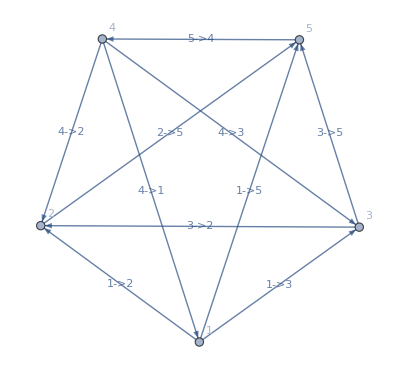

```mathematica
Gin=Graph[{1->2,1->3,4->1,1->5,3->2,4->2,2->5,4->3,3->5,5->4},VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,2.06155,4.94975,5,1.80278,2.91548,2 √5,3.3541,3.04138,3.80789}

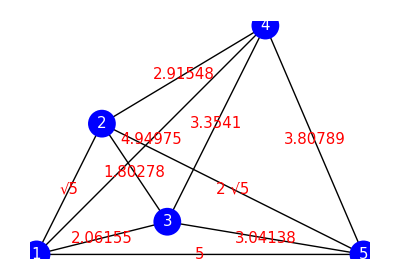

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[PD[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
h=LoopMatrix[Gin]
```

(0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0},{0.,2.06155,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,4.94975,0.,0.,0.,0.,0.,0.,0.},{0,0,0,5,0,0,0,0,0,0},{0.,0.,0.,0.,1.80278,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.91548,0.,0.,0.,0.},{0,0,0,0,0,0,2 √5,0,0,0},{0.,0.,0.,0.,0.,0.,0.,3.3541,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,3.04138,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,3.80789}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
FundLoop
```

{{5<->1,1<->4,4<->5},{5<->1,1<->3,3<->5},{4<->1,1<->3,3<->4},{5<->1,1<->2,2<->5},{4<->1,1<->2,2<->4},{3<->1,1<->2,2<->3}}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[FundLoop[[i]]][[1]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{0,0},{3.5,3.5}},{{5,0},{0,0},{2,0.5}},{{3.5,3.5},{0,0},{2,0.5}},{{5,0},{0,0},{1,2}},{{3.5,3.5},{0,0},{1,2}},{{2,0.5},{0,0},{1,2}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}<0,1,-1],
{i,Length[FundLoop]}](* 右回りならば正、左回りならば負 *)
```

{1,1,-1,1,1,1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[FundLoop[[i]]][[1]]]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Area *)
```

{8.75,1.25,2.625,5,1.75,1.75}

```mathematica
U=Table[-LoopSpin[[i]]FLA[[i]],{i,Length[FundLoop]}](* 誘導起電力行列(誘導起電力は-B'Sに右回りなら1を、左回りなら-1をかける) *)
```

{-8.75,-1.25,2.625,-5,-1.75,-1.75}

```mathematica
RuleFundLoopNew={{1->5,2->1,4->2,5->4},{1->2,2->4,4->1},{1->3,2->1,3->2},{1->2,2->5,5->1},{1->2,2->4,4->3,3->1},{1->3,3->5,5->1}}
```

{{1→5,2→1,4→2,5→4},{1→2,2→4,4→1},{1→3,2→1,3→2},{1→2,2→5,5→1},{1→2,2→4,4→3,3→1},{1→3,3→5,5→1}}

```mathematica
RuleRevFundLoopNew=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoopNew[[i]]]]],
{i,Length[RuleFundLoopNew]}
]
```

{{1→2,5→1,2→4,4→5},{1→4,2→1,4→2},{1→2,3→1,2→3},{1→5,2→1,5→2},{1→3,2→1,4→2,3→4},{1→5,3→1,5→3}}

```mathematica
hNew=Table[
Table[
If[MemberQ[RuleFundLoopNew[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoopNew[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[RuleFundLoopNew]}]
```

{{-1,0,0,1,0,1,0,0,0,1},{1,0,1,0,0,-1,0,0,0,0},{-1,1,0,0,1,0,0,0,0,0},{1,0,0,-1,0,0,1,0,0,0},{1,-1,0,0,0,-1,0,1,0,0},{0,1,0,-1,0,0,0,0,1,0}}

```mathematica
FLPNew=Table[
Pin[[
ConnectedComponents[RuleFundLoopNew[[i]]][[1]]
]],
{i,Length[RuleFundLoopNew]}](* Fundamental Loop Point *)
```

{{{0,0},{5,0},{1,2},{3.5,3.5}},{{0,0},{1,2},{3.5,3.5}},{{0,0},{2,0.5},{1,2}},{{0,0},{1,2},{5,0}},{{0,0},{1,2},{3.5,3.5},{2,0.5}},{{0,0},{2,0.5},{5,0}}}

```mathematica
LoopSpinNew=Table[
If[(Append[FLPNew[[i,2]]-FLPNew[[i,1]],0]×Append[FLPNew[[i,3]]-FLPNew[[i,2]],0]).{0,0,1}<0,1,-1],
{i,Length[RuleFundLoopNew]}](* 右回りならば正、左回りならば負 *)
```

{-1,1,-1,1,1,1}

```mathematica
FLANew=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoopNew[[i]]][[1]]]]
]],
{i,Length[RuleFundLoopNew]}](* Fundamental Loop Area *)
```

{5.08333,1.75,1.75,5,4.375,1.25}

```mathematica
UNew=-LoopSpinNew[[1]]FLANew[[1]]*{1,0,0,0,0,0}(* 誘導起電力行列(誘導起電力は-B'Sに右回りなら1を、左回りなら-1をかける) *)
```

{5.08333,0.,0.,0.,0.,0.}

```mathematica
CurrRemoval=Transpose[hNew].Inverse[hNew.r.Transpose[hNew]].(hNew.s+UNew)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.0244698,0.00842321,0.195607,0.211654,-0.0399834,0.313324,0.248871,0.29384,0.342247,0.802771}

```mathematica
CurrRemoval={-0.0244698343209651,0.008423209759503437,0.1956069045619316,0.2116535291233933,-0.03998340292810969,0.313323993808377,0.24887075655930224,0.2938401045431358,0.34224671723074895,0.8027710029134445}
```

{-0.0244698,0.00842321,0.195607,0.211654,-0.0399834,0.313324,0.248871,0.29384,0.342247,0.802771}

```mathematica
Curr
```

{-0.623285,0.32532,0.348797,0.646762,-0.174382,0.714377,-0.0832895,-0.0679409,0.43176,0.995233}

```mathematica
Curr2=Curr-CurrRemoval
```

{-0.598815,0.316896,0.15319,0.435109,-0.134398,0.401053,-0.33216,-0.361781,0.0895134,0.192462}

```mathematica
Ruleg
```

{1→2,1→3,4→1,1→5,3→2,4→2,2→5,4→3,3→5,5→4}

```mathematica
Gout2=Graph[Table[If[Curr2[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

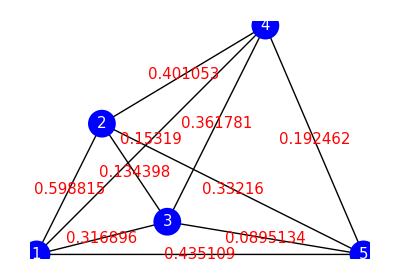

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout2]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr2[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Reverse[Ordering[Abs[Curr2]]]
```

{1,4,6,8,7,2,10,3,5,9}

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```